## ToyScan2

This Mathematica notebook plots the Markov chains obtained by running ToyScan2.  As defined in main.cpp, this scan uses 10 chains and 100k steps to seek out a radius of 3 around the center point (2, 1) with a Gaussian likelihood profile, with uncertainty in the radius 0.3.

### Import and parse the chains

```mathematica
SetDirectory[NotebookDirectory[]];

Chains={};
Module[{i,FileData},
For[i=1,i≤10,i++,
FileData=Import["chains/ToyScan2_chain"<>ToString[i]<>".dat"];
AppendTo[Chains,Split[FileData,#≠{}&]]
]
]
```

```mathematica
Chains[[1,1;;10]]//MatrixForm
```

({1.21776,-5.1825} | {6.23179,1.69665} | {6.31125×10^-26} | {}
{7.04425,5.2149} | {6.57341,0.696066} | {1.55217×10^-31} | {}
{2.51169,5.38781} | {4.41754,1.4547} | {0.0000141824} | {}
{-2.66476,0.449229} | {4.69716,3.02407} | {1.12312×10^-7} | {}
{-2.66476,0.449229} | {4.69716,3.02407} | {1.12312×10^-7} | {}
{2.81658,6.12512} | {5.18976,1.4128} | {2.69597×10^-12} | {}
{5.87087,3.13357} | {4.41992,0.503753} | {0.0000136601} | {}
{5.87087,3.13357} | {4.41992,0.503753} | {0.0000136601} | {}
{5.89859,-1.19311} | {4.47312,0.512419} | {5.80975×10^-6} | {}
{4.92844,-2.3906} | {4.48017,0.858406} | {5.17523×10^-6} | {})

### Setting up accessor functions

```mathematica
ChainLength[iChain_]:=Length[Chains[[iChain]]];

Parameters[iChain_,iPoint_]:=Chains[[iChain,iPoint,1]];
r[iChain_,iPoint_]:=Chains[[iChain,iPoint,2,1]];
θ[iChain_,iPoint_]:=Chains[[iChain,iPoint,2,2]];
NegativeLogLikelihood[iChain_,iPoint_]:=-Log[10,Chains[[iChain,iPoint,3,1]]];
```

### Plotting the chains

Here I plot the full chains, from beginning to end, without burning the initial fraction.  The different colors correspond to different chains.

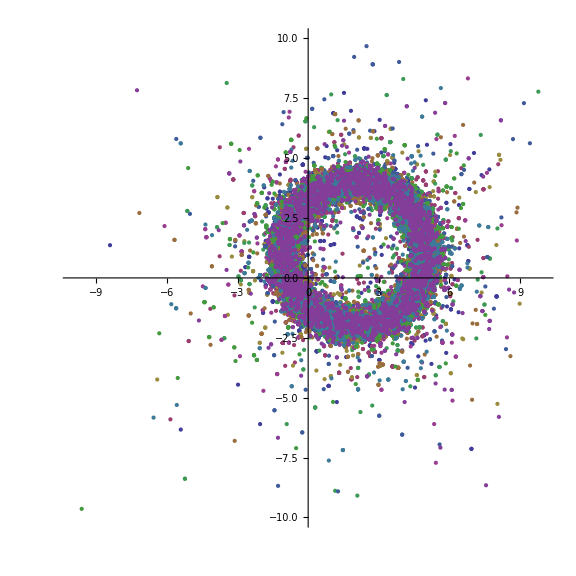

```mathematica
ListPlot[Parameters[All,All],PlotRange->{{-10,10},{-10,10}},AspectRatio->1,ImageSize->Large]
```

Here is what the different sections of the chains look like, as they progress toward the posterior probability distribution.

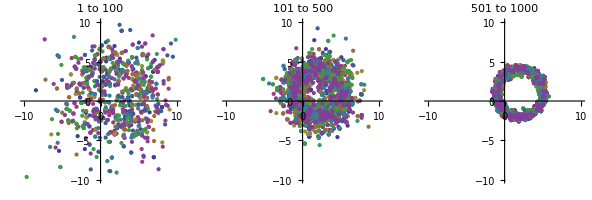

```mathematica
GraphicsRow[{
ListPlot[Parameters[All,1;;100],PlotRange->{{-10,10},{-10,10}},PlotLabel->"1 to 100",AspectRatio->1,ImageSize->Small],
ListPlot[Parameters[All,101;;500],PlotRange->{{-10,10},{-10,10}},PlotLabel->"101 to 500",AspectRatio->1,ImageSize->Small],
ListPlot[Parameters[All,501;;1000],PlotRange->{{-10,10},{-10,10}},PlotLabel->"501 to 1000",AspectRatio->1,ImageSize->Small]
}]
```

### Plotting distance from the center point

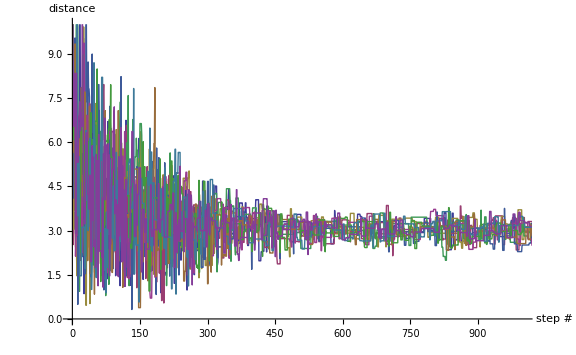

```mathematica
ListPlot[r[All,All],Joined->True,PlotRange->{{0,1000},{0,10}},AxesLabel->{"step #","distance"},ImageSize->Large]
```

### Plotting likelihood

This plots the negative log-likelihood of the points in the chains.  It shows how many orders of magnitude below likelihood == 1.0 (which indicates perfect agreement with the constraint) the likelihood is at.  As the chains’ likelihood increases, the negative log-likelihood approaches zero.

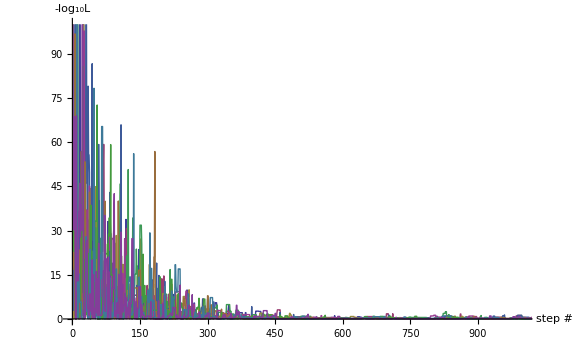

```mathematica
ListPlot[NegativeLogLikelihood[All,All],Joined->True,PlotRange->{{0,1000},{0,100}},AxesLabel->{"step #","-log_10L"},ImageSize->Large]
```